### Categorization

Tutorial

EcoEvo Package

EcoEvo`

EcoEvo/tutorial/Two-SpeciesLotka-VolterraCompetition

### Keywords

Details

# Two-Species Lotka-Volterra Competition

The Lotka-Volterra competition model is one of the simplest competition models.  It is a logical extension of logistic growth to two competing species.

n1'[t]=n1[t](1-(n1[t]+α12 n2[t])/k1)
n2'[t]=n2[t](1-(n2[t]+α21 n1[t])/k2)

k1 and k2 are carrying capacities of species 1 and 2, and α12 and α21 are competition coefficients.

```mathematica
Needs["EcoEvo`"]
```

EcoEvo Package Version 0.9.0α (May 14, 2018)

Set up the model.

```mathematica
SetModel[{
Pop[1]->{Variable->n1,Equation:>dn1},
Pop[2]->{Variable->n2,Equation:>dn2},
Assumptions->{k1>0,k2>0,α12>0,α21>0}
}]

dn1:=n1[t]*(1-(n1[t]+α12 n2[t])/k1);
dn2:=n2[t]*(1-(n2[t]+α21 n1[t])/k2);
```

First, find equilibria.

```mathematica
eq=SolveEcoEq[]
```

{{n1→0,n2→0},{n1→k1,n2→0},{n1→0,n2→k2},{n1→-(k1-k2 α12)/(-1+α12 α21),n2→-(k2-k1 α21)/(-1+α12 α21)}}

Now check linear stability of these equilibria with EcoEigenvalues.

```mathematica
EcoEigenvalues[eq]//NumberedGridForm
```

1 | {1,1}
2 | {-1,(k2-k1 α21)/k2}
3 | {-1,(k1-k2 α12)/k1}
4 | {-((k1-k2 α12) (-k2+k1 α21))/(k1 k2 (-1+α12 α21)),(k1 k2-k1 k2 α12 α21)/(k1 k2 (-1+α12 α21))}

Or simply use EcoStableQ to find conditions for stability.

```mathematica
Simplify[EcoStableQ[eq]]//NumberedGridForm
```

1 | False
2 | Piecewise[{{True, k1 α21>k2}, {False, k1 α21<k2}, {Indeterminate, True}}]
3 | Piecewise[{{True, k2 α12>k1}, {False, k2 α12<k1}, {Indeterminate, True}}]
4 | Piecewise[{{True, (-2 k1 k2+k2^2 α12+k1^2 α21) (-1+α12 α21)>0&&(k1-k2 α12) (-k2+k1 α21) (-1+α12 α21)>0}, {False, (k1-k2 α12) (-k2+k1 α21) (-1+α12 α21)<0||(-2 k1 k2+k2^2 α12+k1^2 α21) (-1+α12 α21)<0}, {Indeterminate, True}}]

Calculate the invasibility of the single-species equilibria.

```mathematica
λ12=Inv[eq⟦3⟧,n1]
λ21=Inv[eq⟦2⟧,n2]
```

1-(k2 α12)/k1

1-(k1 α21)/k2

Notice that these correspond to one of the eigenvalues of the single-species equilibria calculated by EcoEigenvalues above.

Solve for critical values of k1 and k2.

```mathematica
Solve[λ12==0,k1]
Solve[λ21==0,k2]
```

{{k1→k2 α12}}

{{k2→k1 α21}}

Based on mutual invasibility, the outcome of competition is:

k1>k2 α12 && k2<k1 α21 | Case I - species 1 outcompetes species 2
k1<k2 α12 && k2>k1 α21 | Case II - species 2 outcompetes species 1
k1>k2 α12 && k2>k1 α21 | Case III - species 1 & 2 coexist
k1<k2 α12 && k2<k1 α21 | Case IV - founder control
k1==k2 && α12==α21 | Case V - neutrality

Let's plot phase planes and simulate the model for all five of these cases.

### Case I - Species 1 Outcompetes Species 2

```mathematica
α12=α21=1;
k1=1.2;
k2=1;
```

Solve for equilibria.

```mathematica
SolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1→0,n2→0},{n1→1.2,n2→0},{n1→0,n2→1.}}

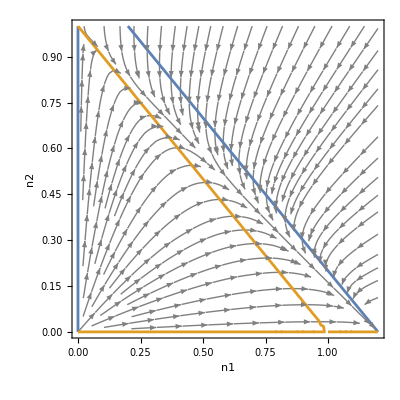

```mathematica
PlotEcoPhasePlane[{n1,0,k1},{n2,0,k2}]
```

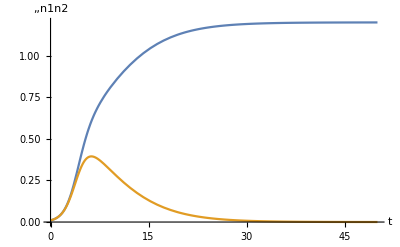

```mathematica
sol=EcoSim[{n1->0.01,n2->0.01},50];
PlotDynamics[sol]
```

### Case II - Species 2 Outcompetes Species 1

```mathematica
α12=α21=1;
k1=1;
k2=1.2;
```

Solve for equilibria.

```mathematica
SolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1→0,n2→0},{n1→1.,n2→0},{n1→0,n2→1.2}}

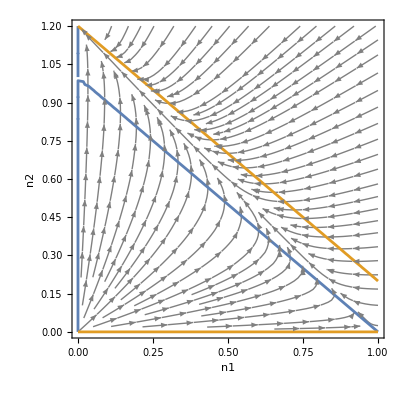

```mathematica
PlotEcoPhasePlane[{n1,0,k1},{n2,0,k2}]
```

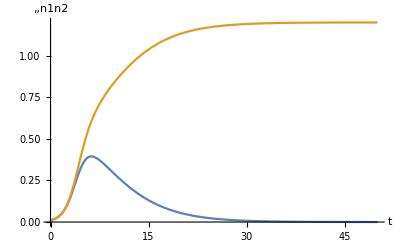

```mathematica
sol=EcoSim[{n1->0.01,n2->0.01},50];
PlotDynamics[sol]
```

### Case III - Species 1&2 Coexist

```mathematica
α12=α21=0.5;
k1=1.2;
k2=1;
```

Solve for equilibria.

```mathematica
eq=SolveEcoEq[]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1→0,n2→0},{n1→1.2,n2→0},{n1→0,n2→1.},{n1→0.933333,n2→0.533333}}

Check stability of the coexistence equilibrium.

```mathematica
EcoEigenvalues[eq⟦4⟧]
```

{-1.,-0.311111}

Both eigenvalues are negative, so the coexistence equilibrium is stable.

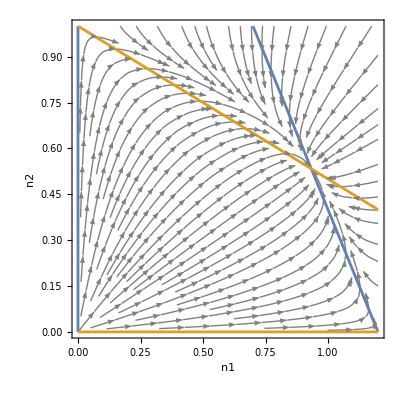

```mathematica
PlotEcoPhasePlane[{n1,0,k1},{n2,0,k2}]
```

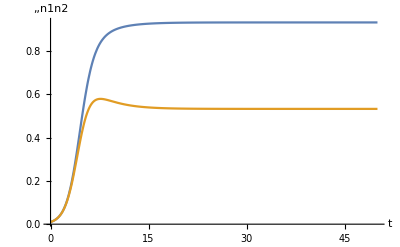

```mathematica
sol=EcoSim[{n1->0.01,n2->0.01},50];
PlotDynamics[sol]
```

### Case IV - Founder Control

```mathematica
α12=α21=2;
k1=1;
k2=1;
```

Solve for equilibria.

```mathematica
eq=SolveEcoEq[]
```

{{n1→0,n2→0},{n1→1,n2→0},{n1→0,n2→1},{n1→1/3,n2→1/3}}

Check stability of the coexistence equilibrium.

```mathematica
EcoEigenvalues[eq⟦4⟧]
```

{-1,1/3}

One positive and one negative eigenvalue indicate that it is an unstable saddle point.

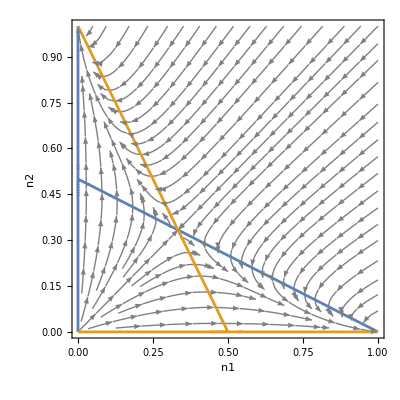

```mathematica
PlotEcoPhasePlane[{n1,0,k1},{n2,0,k2}]
```

Here the outcome depends on the initial conditions.

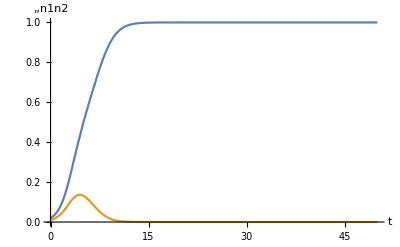

```mathematica
sol=EcoSim[{n1->0.02,n2->0.01},50];
PlotDynamics[sol]
```

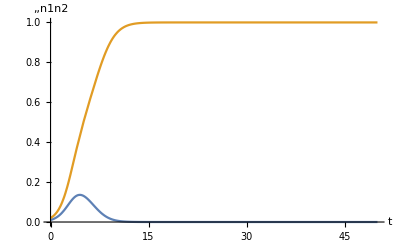

```mathematica
sol=EcoSim[{n1->0.01,n2->0.02},50];
PlotDynamics[sol]
```

### Case V - Neutrality

```mathematica
α12=α21=1;
k1=1;
k2=1;
```

Solve for equilibria.

```mathematica
eq=SolveEcoEq[]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{n2→1-n1},{n1→0,n2→0}}

The first solution is a continuous range of neutrally stable equilibria, which we can verify with EcoEigenvalues.

```mathematica
EcoEigenvalues[eq⟦1⟧]
```

{-1,0}

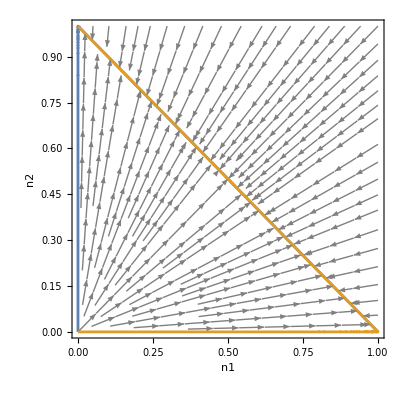

```mathematica
PlotEcoPhasePlane[{n1,0,k1},{n2,0,k2}]
```

Since there is a continuous range of neutrally stable equilibria, the outcome depends continuously on initial conditions.

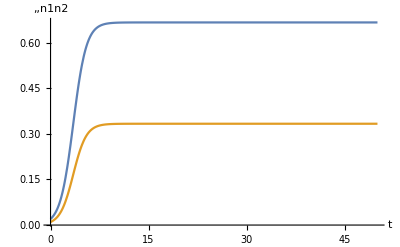

```mathematica
sol=EcoSim[{n1->0.02,n2->0.01},50];
PlotDynamics[sol]
```

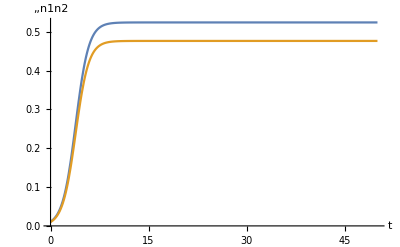

```mathematica
sol=EcoSim[{n1->0.011,n2->0.01},50];
PlotDynamics[sol]
```

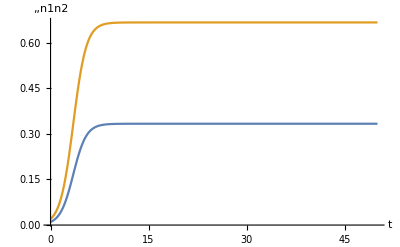

```mathematica
sol=EcoSim[{n1->0.01,n2->0.02},50];
PlotDynamics[sol]
```

## References

More About

Related Tutorials

ExampleModels

Related Wolfram Education Group Courses